## Number of Transactions

```mathematica
start=6191896;

numTXs:=Lookup[BlockchainBlockData[#,BlockchainBase->"Ethereum"], "TotalTransactions"]&

blockReward:=First[Lookup[Lookup[Import["https://beaconcha.in/api/v1/execution/block/"<>ToString[#],"RawJSON"],"data"],"blockReward"]]&

data=Table[{i,numTXs[i],blockReward[i]},{i,start-5,start+20}]
```

{{6191891,68,3018651276715424000},{6191892,90,3017756346621070142},{6191893,164,3132226770614798840},{6191894,127,3086074360315006681},{6191895,124,3046003990534550912},{6191896,92,3076370571290960000},{6191897,103,3031881650000000000},{6191898,25,3126489784077479824},{6191899,34,3147138281643801600},{6191900,10,3182510893000000000},{6191901,15,3176106681020099456},{6191902,46,3155413134000000000},{6191903,6,4503741729000000000},{6191904,3,4520030720000000000},{6191905,7,6959925569000000000},{6191906,3,7008030720000000000},{6191907,4,8914752636000000000},{6191908,5,6995091528600000000},{6191909,166,5137785408402561108},{6191910,108,3101554356377378445},{6191911,200,4301698931775789120},{6191912,90,4930604235739692538},{6191913,283,3108685105396636704},{6191914,84,3324761000000000000},{6191915,129,3157678005931160715},{6191916,168,3089686307500000000}}

## Chart

```mathematica
data=Reverse[data]
blocks=data[[All,1]];
txs=data[[All,2]];
fees=data[[All,3]];
```

{{6191891,68,3018651276715424000},{6191892,90,3017756346621070142},{6191893,164,3132226770614798840},{6191894,127,3086074360315006681},{6191895,124,3046003990534550912},{6191896,92,3076370571290960000},{6191897,103,3031881650000000000},{6191898,25,3126489784077479824},{6191899,34,3147138281643801600},{6191900,10,3182510893000000000},{6191901,15,3176106681020099456},{6191902,46,3155413134000000000},{6191903,6,4503741729000000000},{6191904,3,4520030720000000000},{6191905,7,6959925569000000000},{6191906,3,7008030720000000000},{6191907,4,8914752636000000000},{6191908,5,6995091528600000000},{6191909,166,5137785408402561108},{6191910,108,3101554356377378445},{6191911,200,4301698931775789120},{6191912,90,4930604235739692538},{6191913,283,3108685105396636704},{6191914,84,3324761000000000000},{6191915,129,3157678005931160715},{6191916,168,3089686307500000000}}

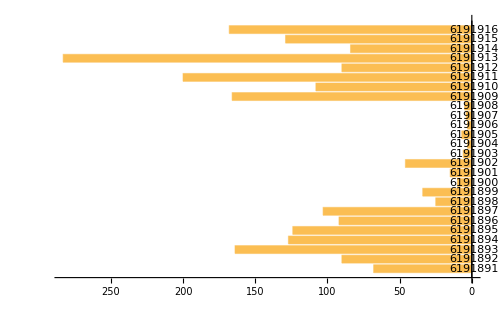

~/Desktop/fig1.pdf

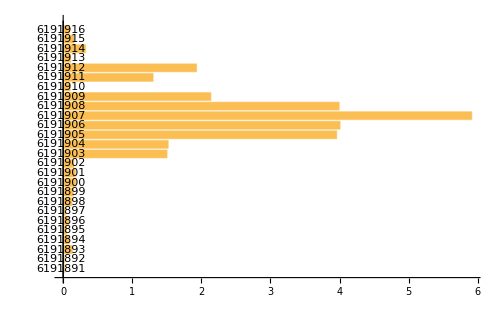

~/Desktop/fig2.pdf

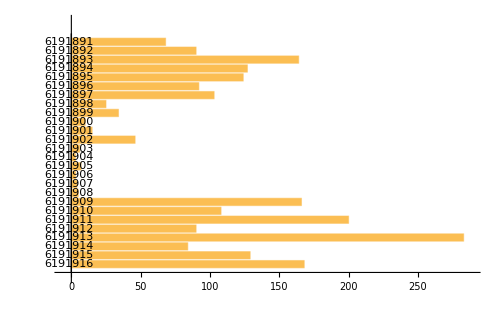

~/Desktop/fig1.png

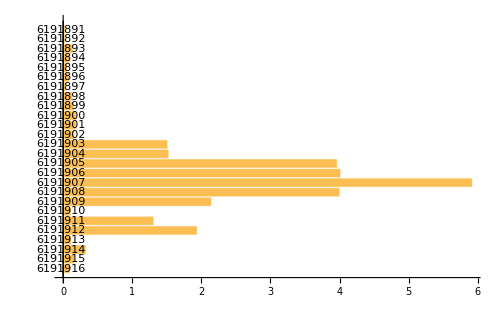

~/Desktop/fig2.png

```mathematica
BarChart[txs,ChartLabels->blocks,BarOrigin->Right,ImageSize->500]
Export["~/Desktop/fig1.pdf",%]
BarChart[fees/(10^18)-3,ChartLabels->blocks,BarOrigin->Left,ImageSize->500]
Export["~/Desktop/fig2.pdf",%]
```